# Template Notebook

Version 1.0, hgrie 15 March 2023  (Short Description, Version History) (nothing to execute)

This notebook produces <very short description>

Underlying manu-script: <main reference>

## Version History and To Do List

### To Do

### Changes in vX.x DATE

## Comments (nothing to execute)

### Explaining Parameters, Conventions

All angles θ are in _XXX_!

### Explanation of observables and kinematics

### Variable Names

### Comments on Fit Procedures

## 0. Preparations + Startup, hgrie: Internal definitions, do not change. EXECUTE BEFORE LOADING .mx FILE!

## This Notebook’s Styles

Note hgrie July 2017 : 
 This notebook feels and smells like the StandardReport.nb style, but it is actually the Default.nb with a few tweaks. 
  Amongst other things, I get around the annoying problems with gray colours in StandardReport.nb.

```mathematica
If[¬($FrontEnd===Null),
SetOptions[EvaluationNotebook[],
CodeAssistOptions->{"FloatingElementEnable"->False},
StyleDefinitions->Notebook[{Cell[StyleData[StyleDefinitions->"Default.nb"]],
(*Following eliminates "Out[]" from printed-output files*)
Cell[StyleData[All,"Printout"],ShowCellLabel->False],
Cell[StyleData["Notebook"],Background->RGBColor[1,0.96,0.90]],
Cell[StyleData["Title"],CellMargins->{{20(*left*),Inherited(*right*)},{0(*bottom*),7(*top*)}}],
Cell[StyleData["Subtitle"],CellMargins->{{40(*left*),Inherited(*right*)},{0(*bottom*),7(*top*)}}],
Cell[StyleData["Subsubtitle"],CellMargins->{{40(*left*),Inherited(*right*)},{0(*bottom*),7(*top*)}}],
Cell[StyleData["Chapter"],FontSize->24,CellFrame->{{0,0},{0,5}},CellMargins->{{20(*left*),Inherited(*right*)},{0(*bottom*),5(*top*)}}],
Cell[StyleData["Subchapter"],FontSize->24,CellFrame->{{0,0},{0,3}},ShowGroupOpener->True,CellDingbat->None,CellMargins->{{40(*left*),Inherited(*right*)},{0(*bottom*),5(*top*)}}],
Cell[StyleData["Section"],FontSize->24,CellFrame->{{0,0},{0,2}},CellFrameColor->RGBColor[0,0,0.5],ShowGroupOpener->True,CellMargins->{{50(*left*),Inherited(*right*)},{7(*bottom*),5(*top*)}}],
Cell[StyleData["Subsection"],ShowGroupOpener->True,CellMargins->{{60(*left*),Inherited(*right*)},{0(*bottom*),5(*top*)}}],
Cell[StyleData["Subsubsection"],ShowGroupOpener->True,CellMargins->{{70(*left*),Inherited(*right*)},{0(*bottom*),5(*top*)}}],
Cell[StyleData["Text"],CellMargins->{{70(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["Item"],MenuCommandKey->"*",CellMargins->{{80(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["Subitem"],CellMargins->{{90(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["Subsubitem"],CellMargins->{{100(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["ItemNumbered"],MenuCommandKey->"+",CellMargins->{{80(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["DisplayFormula"],MenuCommandKey->"(",Background->White,CellMargins->{{70(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["DisplayFormulaNumbered"],MenuCommandKey->")",Background->White,CellMargins->{{70(*left*),Inherited(*right*)},{5(*bottom*),5(*top*)}}],
Cell[StyleData["Input"],CellFrame->{{1,1},{0,1}},CellMargins->{{70(*left*),Inherited(*right*)},{0(*bottom*),7(*top*)}},Background->RGBColor[0.87,0.94,1]],
Cell[StyleData["Output"],CellFrame->{{1,1},{1,0}},CellMargins->{{70(*left*),Inherited(*right*)},{Inherited(*bottom*),0(*top*)}},Background->GrayLevel[1]],
Cell[StyleData["Code"](*mathematica code*),MenuCommandKey->"!",CellMargins->{{70(*left*),Inherited(*right*)},{Inherited(*bottom*),10(*top*)}},Background->Yellow],
Cell[StyleData["Program"](*generic programming code*),MenuCommandKey->"@",CellMargins->{{70(*left*),Inherited(*right*)},{Inherited(*bottom*),10(*top*)}},Background->RGBColor[100/255,149/255,237/255]],
Cell[StyleData["InitializationCell"],MenuCommandKey->"#",CellMargins->{{70(*left*),Inherited(*right*)},{Inherited(*bottom*),10(*top*)}},Background->Green]}(*,StyleDefinitions->"PrivateStylesheetFormatting.nb"*)]]]
```

## Function to Save FrontEnd Notebook

```mathematica
saveNotebook:=If[¬($FrontEnd===Null),NotebookSave[EvaluationNotebook[]]]
```

## Create a Button to Open a Read-Only Version of this File in a New Window

```mathematica
If[¬($FrontEnd===Null),
CreatePalette[Button["Duplicate Active Notebook",NotebookPut[NotebookGet[InputNotebook[]]/.{Rule[DockedCells,_]:>Sequence[],Rule[WindowMargins,_]:>Rule[WindowMargins,{{0,Automatic},{0,Automatic}}],Cell[x___]:>Cell[x,Evaluatable->False]},Background->GrayLevel[0.95],Editable->False,"ClosingSaveDialog"->False,DockedCells->With[{sourcenb=InputNotebook[]},Cell[BoxData[ToBoxes[Button["Update",SelectionMove[InputNotebook[],All,Notebook];
NotebookWrite[InputNotebook[],NotebookGet[sourcenb]/.Cell[x___]:>Cell[x,Evaluatable->False]]]]],"DockedCell",CellContext->Cell]],WindowTitle->"Duplicate of "<>AbsoluteOptions[InputNotebook[],WindowTitle][[1,2]]];
SetSelectedNotebook[InputNotebook[]]],WindowTitle->"Duplicate"];]
```

## Set version number of this file

```mathematica
fileversion=StringForm["v1.0"];
```

## Error Messages, also 3J and 6J symbol error messages switched off

Those are annoying: 	Complaining that one misspelt something, 
			or that the interpolation function is used as extrapolation.

```mathematica
Off[General::"spell"]
Off[General::"spell1"]
Off[InterpolatingFunction::"dmval"]
Off[Clear::"wrsym"]
```

NOTE: 3J and 6J symbold can be summed over unphysical arguments or such which do not fulfill the triangular inequality, like "ThreeJSymbol[{1, -1},{1, -1},{0,2}]", because we just sum blindly. Math...ematica sets the nonsensical MEs to ZERO, so that's fine. This however gives many error messages:

ClebschGordan::"phy": "ThreeJSymbol[{1, -1}, {1, -1}, {1, 2}] is not physical. More…"
ClebschGordan::"tri": "ThreeJSymbol[{0, 0}, {1, 0}, {0, 0}] is not triangular. More…"

In order to avoid that, hgrie switched OFF these error-messages. hgrie checked that the output is the same as Robert's.

```mathematica
Off[ClebschGordan::"phy"]
Off[ClebschGordan::"tri"]
Off[SixJSymbol::"phy"]
Off[SixJSymbol::"tri"]
```

## Package inclusions

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

## Module removeDownValues[] Clear[]s Selected Function Variables (from internet)

```mathematica
SetAttributes[removeDownValues,HoldAllComplete];
removeDownValues[p:f_[___]]:=DownValues[f]=DeleteCases[DownValues[f,Sort->False],HoldPattern[Verbatim[HoldPattern][p]:>_]];
```

Example application:
	removeDownValues[VTews[_,Λ_/;Λ≠Λval,_,_,_,_,_,_]
removes all definitions of VTews which involve as second argument a number which is not Λval.

## Module checkAbort[]: Module to abort a computation when a specific error message is encountered (if no second error message: abort on ANY error/warning)

```mathematica
SetAttributes[checkAbort,HoldFirst]
checkAbort[expr_,HoldPattern[messages_:Sequence[]]]:=Check[expr,Message[checkAbort::abort];Abort[],messages]
checkAbort::abort="Abort[]ing.";
```

Example:

Do[
checkAbort[1/0,Power::infy],
{i,0,4}]

Power::infy: "Infinite expression 1/0 encountered."

checkAbort::abort: "Abort[]ing."

$Aborted

## Plot options

### Plot Look & Feel

#### Colours

```mathematica
red=RGBColor[1,0,0];
green=darkgreen;(*RGBColor[0,1,0];*)
darkgreen=CMYKColor[1,0,1,.5];
blue=RGBColor[0,0,1];
lightblue=RGBColor[5/9,5/9,1];(*=Lighter[Lighter[blue]]*)
darkblue= CMYKColor[1,1,0,.3];
violet=RGBColor[.6,0,1];
white=RGBColor[1,1,1];
black=RGBColor[0,0,0];
fillcolour=lightblue;
grey=GrayLevel[.85];
slidegrey=GrayLevel[.6];
```

Define the “default line style” and “default fill style”

```mathematica
Method/.Charting`ResolvePlotTheme[Automatic,Plot];
defaultlinestyle=("DefaultPlotStyle"/.%)[[1]]
defaultfillstyle=Directive[Append[Table[defaultlinestyle[[i]],{i,1,Length[defaultlinestyle]}],Opacity[0.2]]]
```

Directive[RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6]]

Directive[{RGBColor[0.368417, 0.506779, 0.709798],AbsoluteThickness[1.6],Opacity[0.2]}]

#### Dashing

```mathematica
solid=Dashing[{1,0}]; (*solid*)
dotdashed=Dashing[{0.005,0.02,0.02,0.02}]; (*dot-dashed*)
middashed=Dashing[{0.02,0.02}];(*mid dashed*)
longdashed=Dashing[{0.04,0.02}]; (*long dashed*)
dashed=middashed; (* CHOOSE DASHING!!!!!*)
dotted=Dashing[{0.003,0.015}]; (*dotted*)
```

#### Symbols

using option: PlotMarkers->...

```mathematica
line[colour_,thickness_]:=Graphics/@{{colour,thickness,Circle[{0,0},1]}};
circle[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Circle[{0,0},1]}},size};
disk[colour_,size_]:={Graphics/@{{colour,Disk[{0,0},1]}},size};
andrewscross[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Line[{{1,-1},{-1,1}}],Line[{{1,1},{-1,-1}}]}},size};
cross[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Line[{{1,0},{-1,0}}],Line[{{0,1},{0,-1}}]}},size};
emptytriangle[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Line[{{1,0},{0,Sqrt[3]},{-1,0},{1,0}}]}},size};
filledtriangle[colour_,size_]:={Graphics/@{{colour,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]}},size};emptysquare[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}},size};
filledsquare[colour_,size_]:={Graphics/@{{colour,Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}]}},size};emptydiamond[colour_,thickness_,size_]:={Graphics/@{{colour,thickness,Rotate[Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}],45 Degree,{0,0}]}},size};
filleddiamond[colour_,size_]:={Graphics/@{{colour,Rotate[Polygon[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5}}],45 Degree,{0,0}]}},size};
```

#### Sizes

```mathematica
figimagesize={400*12.5/14.1*10.7/10.6,400/GoldenRatio};
figimagesize2=1.5figimagesize;
```

### Define a Nice Colour Sweep for Plot Styles

Constructed such that the last element always has a solid red line, and the first one is blue

```mathematica
rainbowsweep[n_]:=
Reverse[Table[{(*linestyles*){solid,DotDashed,longdashed,Dashed,Dotted}[[Mod[i,5(*=Length[linestyles]*),1]]],
(*colours*)Table[RGBColor[1.5(x),0,1.5(1-x)],{x,1,0,-1/(n-1)}][[i]]},{i,1,n}]]
```

### Plot Tick Marks

#### Define ticks for logarithmic scale, forcing 10^x as labels

```mathematica
tens=Table[{10.^i,StringForm["10^(``)",i],0.015(*length of tick*),AbsoluteThickness[1.5]},{i,-20,20}];
tensticks=Union[Table[{10.^i,"",0.015(*length of tick*),AbsoluteThickness[1.5]},{i,-20,20}],Flatten[Table[{j 10.^i,""},{i,-20,20},{j,1,9}],1]];
tenstickswithlabel=Union[tens,tensticks];
logtensticks=MapAt[Log,tensticks,{All,1}];(*to adjust ranges inside Show[] for Log plots*)
Clear[tens]
```

#### Define correct ticks for θ ∈[0;180] degree

must do something special since plotGrid somehow makes self-defined Ticks way too large

```mathematica
thetatableup=(*Table[{i,""},{i,0,180,5}]*)Union[Table[{i,"",{0,-0.017}},{i,0,180,30}],Table[{i,""},{i,0,180,5}]]
thetatabledown=(*Union[Table[{i,i},{i,0,180,30}],Table[{i,""},{i,0,180,5}]]*)Union[Table[{i,i (*Degree*),{0,-0.017}},{i,30(*do not display "0" to combine plots more easily*),150(*do not display "150" to combine plots more easily*),30}],Table[{i,""},{i,0,180,5}]]
thetatables={{Automatic,Automatic},{thetatabledown,thetatableup}};
thetatablesx=thetatables;
thetatablesy=thetatables[[{2,1}]];
```

{{0,},{5,},{10,},{15,},{20,},{25,},{30,},{35,},{40,},{45,},{50,},{55,},{60,},{65,},{70,},{75,},{80,},{85,},{90,},{95,},{100,},{105,},{110,},{115,},{120,},{125,},{130,},{135,},{140,},{145,},{150,},{155,},{160,},{165,},{170,},{175,},{180,},{0,,{0,-0.017}},{30,,{0,-0.017}},{60,,{0,-0.017}},{90,,{0,-0.017}},{120,,{0,-0.017}},{150,,{0,-0.017}},{180,,{0,-0.017}}}

{{0,},{5,},{10,},{15,},{20,},{25,},{30,},{35,},{40,},{45,},{50,},{55,},{60,},{65,},{70,},{75,},{80,},{85,},{90,},{95,},{100,},{105,},{110,},{115,},{120,},{125,},{130,},{135,},{140,},{145,},{150,},{155,},{160,},{165,},{170,},{175,},{180,},{30,30,{0,-0.017}},{60,60,{0,-0.017}},{90,90,{0,-0.017}},{120,120,{0,-0.017}},{150,150,{0,-0.017}}}

#### The following takes care of feature when applying plotGrid to plots with θtables: rescale θ axes only --

```mathematica
θPreProcess[table_,yscale_:1(*optional scale on right y axis: if 1, then no numbers, only ticks*)]:=
Table[Module[{plot=table[[i,j]],scale,fticks,gticks},
fticks=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[plot][[2]];
scale=Abs[PlotRange[plot][[2,2]]-PlotRange[plot][[2,1]]]*1.7*10^-4;
gticks=If[yscale==1,Automatic(*i.e if right and left y axes identical, then do not show numbers of right*),
MapAt[#*Sign[yscale]&,MapAt[#*Sign[yscale]/yscale&,fticks,{All,1}],{All,2}]/.{-""->""}];Show[plot,FrameTicks->{{fticks,gticks},{Union[Table[{i,i,{0,-scale}},{i,0,180,30}],Table[{i,""},{i,0,180,5}]],Union[Table[{i,"",{0,-scale}},{i,0,180,30}],Table[{i,""},{i,0,180,5}]]}}]],
{i,1,Dimensions[table][[1]]},{j,1,Dimensions[table][[2]]}]
```

#### Comment: Framelines for ω-dependent plots

FrameTicks→{{Automatic(*left*),Automatic(*right*)},{Automatic(*bottom*),{{((940+140)^2-940^2)/(2*940),"ω_π"}(*,{ωΔ,"ω_Δ"}*)(*top*)}}}},
GridLines→{{ωπ,ωΔ},None},
FrameLabel→{"ω_lab [MeV]","dσ/dΩ [nbarn/sr]"},

#### Comment: Framelines for θ-dependent plots

PlotRange→{{0,180},{0,Automatic}},
FrameTicks→thetatables,
FrameLabel→{"θ_lab [deg]","dσ/dΩ [nbarn/sr]"},

Graphics[Text[Style["ω_lab=55MeV"],Scaled[{0.5,0.2}]]]

### Plot Options Definitions (include using “Evaluate[plotoptions]”)

```mathematica
plotoptions={
PerformanceGoal->"Speed",
Frame->True,
ImageSize-> figimagesize,
FrameStyle->Directive[black,AbsoluteThickness[0.75]](*to make frame and ticks in plots a bit more visible*),TicksStyle->Directive[black,AbsoluteThickness[1]],
GridLinesStyle->Directive[black,AbsoluteThickness[0.75]],
AxesOrigin->{0,0}(*automatically plot axes inside frame; avoids spurious and annoying lines in plots*),
BaseStyle->{Thick (*makes lines thick*),
FontSize->14,
FontFamily->"Times"}};
```

### A typical Plot Legend (comment only)

```mathematica
(*lines=3;
linewidth=35-2.5(lines-1);(*works for 3-5 lines*)
dist=10-0.35(lines-1);(*works for 3-5 lines*)
lineheight=30-2.5(lines-1);(*works for 3-5 lines*)
legend=Show[(*
Graphics[{solid,red,Line[{{0,4lineheight},{linewidth,4lineheight}}],black,Text["",{linewidth+dist,4lineheight},{-1,0}]}],
Graphics[{solid,red,Line[{{0,3lineheight},{linewidth,3lineheight}}],black,Text["",{linewidth+dist,3lineheight},{-1,0}]}],*)
Graphics[{solid,red,Line[{{0,2lineheight},{linewidth,2lineheight}}],black,Text["",{linewidth+dist,2lineheight},{-1,0}]}],
Graphics[{Dashed,blue,Line[{{0,lineheight},{linewidth,lineheight}}],black,Text["",{linewidth+dist,lineheight},{-1,0}]}],
Graphics[{Dotted,green,Line[{{0,0},{linewidth,0}}],black,Text["",{linewidth+dist,0},{-1,0}]}],
BaseStyle->{Thickness[Large],FontSize->14,FontFamily->"Times"(*,Italic*)},AspectRatio->Automatic,ImageSize->{Automatic,(lines-1)*lineheight}]
Clear[lines,linewidth,dist,lineheight]*)
```

to be included via

, Epilog -> Inset[legend, Scaled[{0.6, 0.82}]]

### Module makeLineLegend[] to Produce Plot Legend which only contains lines & text -- include via Show[..., Epilog -> Inset[makeLineLegend[...], Scaled[{0.6, 0.82}]]]

```mathematica
Options[makeLineLegend]=
{LinelengthScale->1(*amount to scale length of drawn line*),
SeparationScale->1(*amount to scale gap between drawn line and text*),
ParskipScale->1(*amount to scale vertical distance between text lines*)};
(**)
makeLineLegend[list_,opts:OptionsPattern[]]:=Module[
{lines=Dimensions[list][[1]](*# of lines*),
linelength(*length of drawn line; works for 3-5 lines*),
separation(*separation between drawn line and text; works for 3-5 lines*),
parskip(*vertical separation between two text text; works for 3-5 lines*),
linelengthscale=OptionValue[LinelengthScale],separationscale=OptionValue[SeparationScale],parskipscale=OptionValue[ParskipScale]},
linelength=(35-2.5(lines-1))*linelengthscale;
separation=(10-0.35(lines-1))*separationscale;
parskip=(30-2.5(lines-1))*parskipscale;
Show[Table[
Graphics[Flatten[{list[[i,1]],Line[{{0,(lines-1-i)parskip},{linelength,(lines-1-i)parskip}}],
(*black,*)Text[list[[i,2]],{linelength+separation,(lines-1-i)parskip},{-1,0}]}]],
{i,1,lines}],
BaseStyle->{Thickness[Large],FontSize->14,FontFamily->"Times"(*,Italic*)},AspectRatio->Automatic,ImageSize->{Automatic,(lines-1)*parskip*parskipscale}]]
```

example:

{{{Dashing[{1,0}],RGBColor[1, 0, 0]},one},{{Dashing[{Small,Small}],RGBColor[0, 0, 1]},two},{{Dashing[{0,Small}],CMYKColor[1, 0, 1, 0.5]},three}}

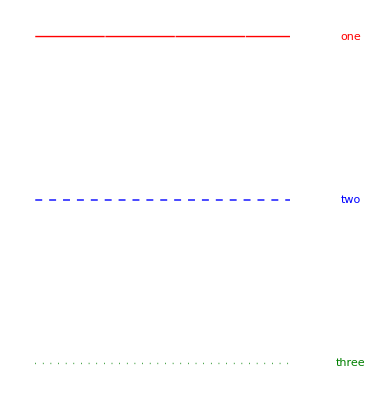

```mathematica
{{{solid,red},"one"},{{Dashed,blue},"two"},{{Dotted,green},"three"}}
makeLineLegend[%,LinelengthScale->1.3]
```

### Module makeLegend[] to Produce Plot Legend which contains user-specified symbols & text -- include via Show[..., Epilog -> Inset[makeLineLegend[...], Scaled[{0.6, 0.82}]]]

```mathematica
Options[makeLegend]=
{LinelengthScale->1(*amount to scale length of drawn line*),
SeparationScale->1(*amount to scale gap between drawn line and text*),
ParskipScale->1(*amount to scale vertical distance between text lines*)};
(**)
makeLegend[list_,opts:OptionsPattern[]]:=Module[
{lines=Dimensions[list][[1]](*# of lines*),
linelength(*length of drawn line; works for 3-5 lines*),
separation(*separation between drawn line and text; works for 3-5 lines*),
parskip(*vertical separation between two text text; works for 3-5 lines*),
linelengthscale=OptionValue[LinelengthScale],separationscale=OptionValue[SeparationScale],parskipscale=OptionValue[ParskipScale]},
linelength=(35-2.5(lines-1))*linelengthscale;
separation=(10-0.35(lines-1))*separationscale;
parskip=(30-2.5(lines-1))*parskipscale;
Show[Table[
Graphics[Flatten[{list[[i,1]],Text[list[[i,2]],{linelength+separation,(lines-1-i)parskip},{-1,0}]}]],
{i,1,lines}],
BaseStyle->{Thickness[Large],FontSize->14,FontFamily->"Times"(*,Italic*)},AspectRatio->Automatic,ImageSize->{Automatic,(lines-1)*parskip*parskipscale}]]
```

example:

{{{Dashing[{1,0}],RGBColor[0.368417, 0.506779, 0.709798],Disk[{5,40},4],AbsoluteThickness[1],Line[{{0,10},{20,10}}]},^4He HIγS data at 61MeV},{{Dashing[{1,0}],RGBColor[1, 0, 0],Line[{{30,10},{40,10}}]},^3He}}

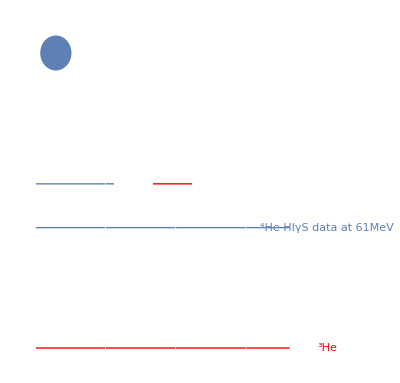

```mathematica
{{{solid,RGBColor[0.368417,0.506779,0.709798],Disk[{10/2,40},4],AbsoluteThickness[1],
Line[{{0,10},{20,10}}]},"^4He HIγS data at 61MeV"},
{{solid,red,Line[{{30,10},{40,10}}]},"^3He"}}
makeLineLegend[%,LinelengthScale->2]
```

## Module for small-sized graphics in .pdf

old file size with poor rendering was 0.25MB. With much better rendering, we now get same size (using rastered output).
option “magnification” (last argument) increases resolution quality but increases filesize -- starts to sputter when set to 4 or more.

```mathematica
rasteredexport[filename_,plotname_,resolution_(*300 is well enough for good ressolution; 450 is quite perfect*),imagesize_]:=
Export[filename,plotname,"AllowRasterization"->True,ImageSize->imagesize(*360*),ImageResolution->resolution]
```

another way was the following, but it produced garbage if figure too complicated (like clover-plot).

```mathematica
(*rasteredexport[filename_,plotname_,magnification_:3]:=
Export[filename,plotname,Rasterize[Magnify[plotname,magnification(*magnification of 3 looks fine on hgrie's terminal, with acceptable filesize*)],"Image"],ImageResolution->600(*no noticeable difference with this option*)]*)
```

## Module PlotGrid from Function Repository 20 Nov 2020

```mathematica
PlotGrid=ResourceFunction["PlotGrid"]
```

```mathematica
PlotGrid[Partition[Table[Plot[x^n,{x,-2,2},Evaluate[plotoptions]],{n,0,5}],2]]
```

-Graphics-

### Documentation

PlotGrid[{{plt_(1,1),…},…}]

arranges the given matrix of plots into a grid where adjacent plots share the frame ticks.

PlotGrid enables the creation of plots with shared frame ticks.

In PlotGrid[{[plt_(1,1),…},…}], the plt_(i,j) can be Graphics expressions or Legended graphics expressions.

SpanFromLeft, SpanFromAbove and SpanFromBoth can be used in place of the plt_(i,j) to create spanning plots, as is possible for Grid.

The plt_(i,j) can also be Null or None, in which case the corresponding grid space is left empty.

PlotGrid automatically hides frame ticks and labels on shared edges.

The graphics returned by PlotGrid is freely resizable, with all plots scaling appropriately.

PlotGrid accepts the same options as Graphics, with the following additions and changes:

AspectRatio | Automatic | aspect ratio of the plot grid
FrameLabel | None | outer frame labels, shared by all plots of the grid
FrameStyle | Automatic | the style of the outer frame and labels
ItemSize | Automatic | the size of the rows and columns
Spacings | None | the spacing to leave between the rows and columns
PlotLabels | None | how to label the individual plots
LabelingFunction | Automatic | post-processing function for plot labels
"ShowFrameLabels" | Full | which frame labels and tick labels of the plots to show
"HideOuterTickLabels" | Full | whether to hide outer tick labels to prevent overlaps
"MergeAxes" | False | whether to merge axes by connecting the frames of adjacent plots
PerformanceGoal | "Quality" | whether to favor graphics that are fast to render or look better
Method | Automatic | advanced options to use

In addition to all standard settings, the following settings can be given for AspectRatio:

Automatic | automatic value based on the ItemSize setting and aspect ratios of invididual plots
GeometricMean | use the geometric mean of all aspect ratios as AspectRatio
Mean | use the arithmetic mean of all aspect ratios as AspectRatio

With the default setting AspectRatio→Automatic, multiplying the ItemSize specifications for one dimension by a number scales the aspect ratio by the same amount.

The labels specified by FrameLabel are drawn outside potential frame labels of the inner plots.

With the default setting FrameStyle→Automatic, the style is inherited from the first plot of the grid.

For ItemSize, the following settings can be given for an individual row/column:

Automatic | use a constant default size
size | use the specified size relative to other rows/columns
Scaled | size item relative to the plot range
ImageScaled | size item relative to the image size
Scaled[s] | size by plot range, scaled by a factor s
ImageScaled[s] | size by image size, scaled by a factor s
Offset[size] | size in printers points
Offset[offset,spec] | add offset printers points to the size specified by spec

For ItemSize, the setting Automatic is equivalent to specifying 1.

The settings Scaled and ImageScaled for ItemSize are equivalent to Scaled[1] and ImageScaled[1], respectively.

Specifying n for one item and Automatic for the remaining ones causes it to be n times as big as the rest.

When different types of scalings, e.g. Scaled and ImageScaled[2], are mixed, PlotGrid effectively tries to convert all specifications to pure size specifications with reasonable conversion factors.

At least one row and one column must use a relative ItemSize setting.

Reference sizes for Scaled and ImageScaled type specifications are only computed from non-spanning plots and can therefore not be used for rows/columns where every plot is spanning.

For Spacings, the following settings can be given for an individual gap between rows/columns:

size | size in printers points
Scaled[s] | fraction s of the plot grid width

The options ItemSize and Spacings support the full range of sequence specifications described in the respective documentation pages.

For PlotLabels, the following settings can be given:

None | add no labels
spec | use the same specification for all plots
{spec_1,…} | use different specifications for each plot
{{spec_(1,1),…},…} | use several labels for a plot
{{{spec_(1,1,1),…},…},…} | use several top-level label lists
Placed[{…},pos] | place labels at the specified position

In PlotLabels→spec, Placed wrappers can be placed at any level to specify label positoning, with the innermost specification taking precedence.

The form PlotLabels→ {{{spec_(1,1,1),…},…},…} is useful in the form PlotLabels->{spec,{{spec_(1,1,1),…},…}}, where spec is applied to all plots, and the spec_(i,j,k) are applied to individual plots plot_j.

In case of ambiguity, label specifications given as nested lists are interpreted as several labels per plot instead of multiple top-level label lists. To ensure the specification is interpreted differently, an empty specification of the form {{}} can be added, as in PlotLabels->{spec,{spec_(1,1),…},{{}}}.

In PlotLabels, the following settings can be given for an individual label specification:

Column→format | automatically number plot based on format, with plots ordered by columns
Row→format | number plots ordered by rows
lbl | use lbl as label
Placed[spec,pos] | place label at the specified position

For PlotLabels, Automatic→format is equivalent to Column→format.

In type→format type PlotLabels specifications, the format can be a string or wrapped string, where the first letter/number is replaced by the corresponding number for each plot based on the following table:

a | number plots using a, b, c, …
A | number plots using A, B, C, …
i | number plots using i, ii, iii, …
I | number plots using I, II, III, …
1 | number plots using 1, 2, 3, …

The position in Placed[spec,pos] type PlotLabels specifications supports similar settings as used by PlotLegends placement; in particular, the following settings can be used:

Left,Above,… | symbolic specifications
{x,y} | explicit settings for horizontal and vertical positioning
ImageScaled[{x,y}] | numeric position which does not try to avoid the frame of the plots
Offset[{dx,dy},spec] | position offset by the specified number of printers points

For numeric position specifications, values below 0 are left of/below the plot, values above 1 are right of/above the plot, and values in between are inside the plot frame.

If no position is specified for a label, {Left,Top} is used as default.

By default, label placement tries to avoid the frame of the plot, placing labels either inside the plot range or outside the frame. Using ImageScaled[pos] type coordinates overrides this behavior.

Labels can also be specified for individual plots using Labeled wrappers of the form Labeled[plot,lbl,…].

For LabelingFunction, the following settings can be given:

Automatic | automatically combine labels vertically or horizontally
func | use func to arrange labels
(Automatic→func) | wrap the arranged labels with func

In LabelingFunction→func, func is called with a list of all labels for each position.

In LabelingFunction→(Automatic→func), func is called with a single row/column construct that contains all labels for a given position.

For "ShowFrameLabels", the following settings can be given for an individual plot:

Automatic | show frame labels if there is no adjacent plot
Full | show frame labels if there is a gap or no adjacent plot
All or True | show all frame labels
None or False | show no frame labels
{hspec,vspec} | use separate settings for the horizontal and vertical frame edges
{{left,right},{bottom,top}} | use different settings for each side
{side_1→spec_1,…} | use the specified setting for the specified side
{def,side_1→spec_1,…} | use def for sides where no explicit value is given

The option "ShowFrameLabels" supports the same specifications to specify individual items as described in the documentation of ItemStyle.

In the setting for "ShowFrameLabels", Directive can be used instead of List to indicate that a specification should be interpreted as one instead of a sequence for different items.

In "ShowFrameLabels" settings, the side_i can be Left, Right, Top or Bottom.

With the default setting "ShowFrameLabels"→Full, labels are hidden for grids with merged axes, but stay visible for layouts with spacing between the plots.

The options "HideOuterTickLabels" and "MergeAxes" operate on the boundaries between rows/columns of plots and support the same sequence specifications as described for Spacings.

For each pair of neighboring rows/columns, the following settings can be given for "HideOuterTickLabels":

sideSpec | Automatic | which sides the hiding should be applied to
methodSpec | Full | when to apply the hiding based on the existence of neighboring plots and spacings
threshold | Automatic | up to which distance from the edge to hide individual tick labels
{sideSpec,methodSpec,threshold} | {Automatic,Full, Automatic} | specify values for all three parts of the setting

In {sideSpec,methodSpec,threshold}, any subset of the settings can be omitted, e.g. {sideSpec,threshold} or {methodSpec} are both valid.

The hiding strategy for "HideOuterTickLabels" consists of three steps: For each pair of neighboring rows/colums, decide to which side(s) (if any) to apply the hiding based on sideSpec. Look whether there is a neighboring plot or spacing, and decide whether still to hide tick labels based on methodSpec. Use threshold to hide the tick labels that are too close to the edge.

In "HideOuterTickLabels"→{sideSpec,…}, the following settings can be given for sideSpec:

Automatic | hide the tick labels on the bottom/left plots
First | hide the tick labels on the plots that appear first in the grid
Last | hide the tick labels on the plots that appear last in the grid
All or True | hide on both sides
None or False | hide none of the labels

Left and Top can be used in place of First for increased readability. Similarly, Right and Bottom can be used instead of Last.

In "HideOuterTickLabels"→{…,methodSpec,…}, the following settings can be given for methodSpec:

Automatic | apply hiding everywhere there is a neighboring plot
Full | apply hiding only if there is a neighboring plot with no spacing
All or True | apply hiding to all sides
None or False | do not apply hiding to any side

In "HideOuterTickLabels"→{…,threshold}, the following settings can be given for threshold:

Automatic | automatically choose threshold
thres | a distance threshold in printers points
Scaled[thres] | a distance threshold as a fraction of the plot range

A threshold setting of Automatic is equivalent to 10 with PerformanceGoal→"Quality" and -∞ with PerformanceGoal→"Speed".

The default setting "HideOuterTickLabels"→Full is equivalent to specifying {Automatic,Full,Automatic} and hides the tick labels of directly adjacent plots (on the left/bottom plot respectively) if they are closer than 10 printers points from the edge, assuming PerformanceGoal→"Quality" is set.

The distance check for thresholds given in printers points is made assuming the initial size of the grid and may not be accurate if the grid is resized afterwards.

In case of ambiguity, settings are always interpreted as methodSpec first instead of sideSpec. This means that "HideOuterTickLabels"→All is equivalent to {Automatic,All,Automatic}, and not {All,Full,Automatic}.

For each pair of neighboring rows/columns, the following settings can be given for "MergeAxes":

False | do not merge the axes
"type" | use a named merge indicator
"type"→size | use the specified size for the merge indicator
{expr_1,expr_2} | use the specified expression as merge indicators on either size of the gap
{expr,Automatic} | use a rotated version of one expression for both sides
expr | use a single expression
{spec,width} | specify the width of the indicator in printers points
None | draw no extra primitives

The following named merge indicators are supported:

"ZigZag" | 
"Cut" | 
"Wave" | 
"Dotted" | 
"Line" |

In "type"→size, the size specifies the length of the feature (e.g. the length of the dashed line) of the indicator in printers points. The default size is 10 printers points.

The merge indicator inherits the style from the frames of the two plots, with each half inheriting the style of the respective plot. For expr type specifications, the style of the left/top plot is inherited.

In general, any expression can be used as merge indicator. For proper alignment, a Graphics expression should be used, with the {0,0} point at the point where the primitive connects to the frame. To ensure sizing works as expected, AspectRatio→Full should be set.

Due to antialiasing, the alignment of the merge indicators might not be perfect for all sizes of the resulting plot grid. Resizing it slightly will fix the issue in those cases.

In the settings for "HideOuterTickLabels" and "MergeAxes", Directive can be used instead of List to indicate that a specification should be interpreted as one instead of a sequence for different items.

For "ShowFrameLabels", "HideOuterTickLabels" and "MergeAxes", settings can be specified on a per-plot basis using Frame[plot,opts] type wrappers, e.g. Frame[plot,"ShowFrameLabels"→None].

For PerformanceGoal, the following settings can be given:

"Quality" | Favor high-quality results over fast-to-render ones
"Speed" | Reduce number of custom frame ticks to improve resizing performance

The setting of PerformanceGoal affects the defaults of the "HideOuterTickLabels" threshold and of the "AllCustomTicks" Method suboption.

The following Method suboptions can be given:

"FixFrameTicks" | True | whether to attempt to fix the length of custom ticks
"AllCustomTicks" | Automatic | whether to use custom ticks for all frame ticks

With the default setting "FixFrameTicks"→True, the tick lengths of custom tick specifications are rescaled to work around a bug caused by using AspectRatio→Full with custom ticks.

The workaround used by "FixFrameTicks"→True estimates the effective aspect ratio of the plots, and may therefore result in suboptimal results if the grid is significantly resized after creation.

The setting "AllCustomTicks" can be used to control whether a custom tick function should be used for all sides that are set to Automatic, True or All to ensure a more uniform result. This might be necessary since the ticks generated by those settings cannot be fully reproduced in all cases.

The default setting "AllCustomTicks"→Automatic uses custom ticks only in the event that any default tick specification already needed to be replaced, e.g. to hide the outer tick labels, and only if PerformanceGoal→"Quality" is set.

PlotGrid returns a Graphics expression or a Legended graphics expression.

PlotGrid will move all legends that are outside of the individual plots to the outside of the entire grid, while leaving those inside in place.

PlotGrid sets CoordinatesToolOptions to enable extraction of coordinates from any of the plots. The format of the points is {{i,j},{x,y}}, where i,j are the indices of the plot and x,y the coordinates in the coordinate system of the plot.

## Module: figures in Column, Row or Array to have same (frame) size: alignedGraphicsColumn/Row/Array[list,opts]

hgrie July 2017
mostly from https://mathematica.stackexchange.com/questions/88312/remove-the-extra-white-space-padding-introduced-by-implicit-use-of-inset-in-grap , 
but added Row and more examples how to get good grids for Array

#### Define auxiliary functions

```mathematica
padding[g_Graphics]:=With[{im=Image[Show[g,LabelStyle->White,Background->White]]},BorderDimensions[im]]
leftRightPadding[graphicsSequence__Graphics]:={1+Max/@Transpose@(First/@#)&@(padding/@List@graphicsSequence),{Automatic,Automatic}}
maxPadding[graphicsSequence__Graphics]:=1+{Max/@Transpose@(First/@#),Max/@Transpose@(Last/@#)}&@(padding/@List@graphicsSequence)
```

### Define function to align several graphics into same sizes in a column: alignedGraphicsColumn[list,opts]

Explain Options:
 Accepts Graphics options for the whole image.

In the current implementation, ImageSize is broken, but it's functionality is mimicked with:

SubImageWidth: an option that determines the figure width.
        Choosing a positive real number x mimics the behavior of ImageSize -> x.
        Full scales all of the sub-plots so that they all have the width of the sub-plot with the largest width, and the ImageSize is then this width.
        Automatic is the default: the ImageSize is the width of the sub-plot with the largest width.

FrameAligned determines the alignment functionality.
        All: all plots get the same ImagePadding, and so the plots get lined up nicely, with lots of space between them, which can be fixed with Spacings.
        LeftOnly: all plots get the same ImagePadding on the left and the right, which aligns the left sides of the frames only, unless all sub-plots have the same ImageSize.
        None: applies no ImagePadding, so the plots do not line up.

Spacings: works as advertised in GraphicsGrid and related functions.

#### Define function alignedGraphicsColumn[list_,opts:OptionsPattern[]]

```mathematica
Clear[alignedGraphicsColumn]
(*options*)
Options[alignedGraphicsColumn]=Join[{Spacings->0,FrameAligned->LeftOnly,SubImageWidth->Automatic},Options[Graphics]];
(*error message texts*)
alignedGraphicsColumn::faligned="Value of option FrameAligned is not All, None, or LeftRight.";
alignedGraphicsColumn::width="Value of option SubImageWidth is not Full, Automatic, or a positive machine number.";
(**)
alignedGraphicsColumn[list_,opts:OptionsPattern[]]:=Module[{sizes,width,plots,optWidth=OptionValue[SubImageWidth]},Which[And[optWidth=!=Automatic,optWidth=!=Full,!NumericQ@optWidth],Return[Message[alignedGraphicsColumn::width]],optWidth===Automatic,plots=list,optWidth===Full,plots=Show[#,ImageSize->Max@First@(ImageDimensions/@list)]&/@list,NumericQ@optWidth,Which[!Element[optWidth,Reals],Return[Message[alignedGraphicsColumn::width]],optWidth≤0,Return[Message[alignedGraphicsColumn::width]],optWidth>0,plots=Show[#,ImageSize->optWidth]&/@list],True,plots=list];Which[And@@(OptionValue[FrameAligned]=!=#&/@{LeftOnly,All,None}),Return[Message[alignedGraphicsColumn::faligned]],OptionValue[FrameAligned]===LeftOnly,plots=Show[#,ImagePadding->leftRightPadding@@plots]&/@plots,OptionValue[FrameAligned]===All,plots=Show[#,ImagePadding->maxPadding@@plots]&/@plots,OptionValue[FrameAligned]===None,True];sizes=ImageDimensions/@plots;width=Max@sizes[[All,1]];sizes=sizes[[All,2]]+Join[{0},ConstantArray[OptionValue[Spacings],Length@plots-1]];Graphics[Table[Inset[plots[[i]],{0,-Plus@@sizes[[;;i]]},ImageScaled[{0,0}]],{i,Length[plots]}],ImageSize->{width,Plus@@sizes},ImagePadding->None,PlotRange->{{0,width},{-Plus@@sizes,0}},AspectRatio->Plus@@sizes/width,PlotRangePadding->None,FilterRules[{opts},Options[Graphics]]]]
```

#### Example

```mathematica
(*p1=Plot[x,{x,0,1},Frame->True,FrameLabel->{None,"left"},BaseStyle->{FontSize->10},ImageSize->300];
p2=Plot[x^2,{x,0,1},Frame->True,FrameLabel->{{None,"right"},{"bottom",None}},BaseStyle->{FontSize->10},ImageSize->255,AspectRatio->1];
p3=Plot[(x-1)^3,{x,0,1},Frame->True,FrameLabel->{"bottom",None},BaseStyle->{FontSize->10},ImageSize->255];
alignedGraphicsColumn[{p1,p2,p3},FrameAligned->All,SubImageWidth->200,Spacings->20,Background->LightBlue]
alignedGraphicsColumn[{p1,p2,p3},FrameAligned->LeftOnly,SubImageWidth->Automatic,Spacings->20]
alignedGraphicsColumn[{p1,p2,p3},FrameAligned->LeftOnly,SubImageWidth->Full]
alignedGraphicsColumn[{p1,p2,p3},FrameAligned->None]
Clear[p1,p2,p3]*)
```

### Define function to align several graphics into same HEIGHTS in a row: alignedGraphicsRow[list,opts]

```mathematica
Clear[alignedGraphicsRow]
(*options*)
Options[alignedGraphicsRow]=Join[{Spacings->0,ImageWidth->Automatic},Options[Graphics]];
(*error messge text*)
alignedGraphicsRow::width="Value of option ImageWidth is not Automatic or a positive machine number.";
(**)
alignedGraphicsRow[list_,verticalSize_:250(*need to specify vertical size; defult is 250*),opts:OptionsPattern[]]:=
Module[{p1h,p1v,p2h,p2v,verticalPadding,newlist},
newlist=Table[Show[list[[i]],ImageSize->{Automatic,verticalSize}],{i,1,Length[list]}];
Do[{ph[i],pv[i]}=padding[newlist[[i]]],{i,1,Length[newlist]}];
verticalPadding=Max/@Transpose[Table[pv[i],{i,1,Length[newlist]}]];
Row[Table[Show[newlist[[i]],ImagePadding->{ph[i],verticalPadding}],{i,1,Length[newlist]}]]]
```

#### Example: when both plots have same AspectRatio, then plot frames are actually also drawn at same size!

```mathematica
(*plot1=Plot[x^2,{x,0,1},Frame->True,FrameLabel->{"x (nm)","y (nm)"},BaseStyle->{FontFamily->"Arial",20},ImageSize->{Automatic,verticalSize}];
plot2=Plot[x^2,{x,-10,10},PlotRange->{-10,1000},Frame->True,FrameLabel->{"x^2",None},BaseStyle->{FontFamily->"Arial",20},AspectRatio->1,ImageSize->{Automatic,verticalSize}];
plot3=Plot[x^2,{x,-100,100},PlotRange->{-10,100000},Frame->True,FrameLabel->{"x^2",None},BaseStyle->{FontFamily->"Arial",20},ImageSize->{Automatic,verticalSize}];
alignedGraphicsRow[{plot1,plot2}]
alignedGraphicsRow[{plot1,plot3}]
alignedGraphicsRow[{plot1,plot2},150]
alignedGraphicsRow[{plot1,plot3},150]
Clear[plot1,plot2,plot3]*)
```

### Define function to align several graphics into same sizes in an array: alignedGraphicsGrid[list,opts]

#### Define function alignedGraphicsGrid[list,opts]

```mathematica
Clear[alignedGraphicsGrid]
(*options*)
Options[alignedGraphicsGrid]=Join[{Spacings->0,ImageWidth->Automatic},Options[Graphics]];
(*error messge text*)
alignedGraphicsGrid::width="Value of option ImageWidth is not Automatic or a positive machine number.";
(**)
alignedGraphicsGrid[list_,opts:OptionsPattern[]]:=Module[{size,sizes,width,height,plots,space=OptionValue[Spacings],optWidth=OptionValue[ImageWidth]},plots=Map[Show[#,ImagePadding->maxPadding@@Flatten@list]&,list,{2}];size=ImageDimensions@plots[[1,1]];sizes=space {Range[0,Last@#]/.{a___,b_,c_}:>{a,b,b},Range[0,First@#]}+size {Range[0,Last@#],Range[1+First@#]}&@Dimensions@plots;Which[And[optWidth=!=Automatic,!NumericQ@optWidth],Return[Message[alignedGraphicsGrid::width]],NumericQ@optWidth,plots=Map[Show[#,ImageSize->optWidth/sizes[[1,-1]] ImageDimensions[#][[1]]]&,plots,{2}];sizes=sizes*optWidth/sizes[[1,-1]],optWidth===Automatic,plots=list];height=sizes[[2,-2]];width=sizes[[1,-1]];Graphics[MapThread[Inset[#1,#2,ImageScaled[{0,0}]]&,{plots,Transpose@Outer[List,sizes[[1, ;;-2]],-sizes[[2, ;;-2]]]},2],ImageSize->{sizes[[1,-1]],height},ImagePadding->None,PlotRange->{{0,width},{-height,0}},AspectRatio->height/width,PlotRangePadding->None,FilterRules[{opts},Options[Graphics]]]]
```

#### Examples

```mathematica
(*p1=Plot[x,{x,0,1},Frame->True,FrameLabel->{None,"left"},BaseStyle->{FontSize->10},ImageSize->300];
p2=Plot[x^2,{x,0,1},Frame->True,FrameLabel->{{None,"right"},{"bottom",None}},BaseStyle->{FontSize->10},ImageSize->255,AspectRatio->1];
p3=Plot[(x-1)^3,{x,0,1},Frame->True,FrameLabel->{"bottom",None},BaseStyle->{FontSize->10},ImageSize->255];*)
```

It does NOT work out of the box:

```mathematica
(*alignedGraphicsGrid[{{p1,p2},{p3,p1},{p1,p1}}/.HoldPattern[FrameLabel->_]:>Sequence[](*eliminates all frame labels*),
Spacings->{-22,-20}(*needs fine tuning*),ImageWidth->400]*)
```

```mathematica
(*alignedGraphicsGrid[{{p1,p2},{p3,p1},{p1,p1}},Spacings->{-22,-20}(*needs fine tuning*),ImageWidth->400]*)
```

But I can fix that:

```mathematica
(*commonimagesize=200;commonaspectratio=1/GoldenRatio;
alignedGraphicsGrid[{
{Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p2,ImageSize->commonimagesize,AspectRatio->commonaspectratio]},
{Show[p3,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio]},
{Show[p3,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio]}}(*/.HoldPattern[FrameLabel->_]:>Sequence[](*eliminates all frame labels*)*),
Spacings->{-22,-20}(*needs fine tuning*),ImageWidth->2*commonimagesize]
Clear[commonimagesize,commonaspectratio]*)
```

To eliminate frame labels, activate line “/.HoldPattern[FrameLabel→_]:>Sequence[]”:

```mathematica
(*commonimagesize=200;commonaspectratio=1/GoldenRatio;
alignedGraphicsGrid[{
{Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p2,ImageSize->commonimagesize,AspectRatio->commonaspectratio]},
{Show[p3,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio]},
{Show[p3,ImageSize->commonimagesize,AspectRatio->commonaspectratio],Show[p1,ImageSize->commonimagesize,AspectRatio->commonaspectratio]}}/.HoldPattern[FrameLabel->_]:>Sequence[](*eliminates all frame labels*),
Spacings->{-22,-20}(*needs fine tuning*),ImageWidth->2*commonimagesize]
Clear[commonimagesize,commonaspectratio]*)
```

and now something fancy: without any frame labels:

```mathematica
(*numberofColumns=2;imagesize=600;commonaspectratio=1/GoldenRatio;
plotlist={p1,p2,p1,p3,p3,p3};
Module[{firstinlastrow,polstableforPlot,commonimagesize=imagesize/numberofColumns},
firstinlastrow=(Dimensions[Partition[plotlist,numberofColumns]][[1]]-1)*numberofColumns+1;
polstableforPlot=Flatten[Transpose[Partition[plotlist,Dimensions[Partition[plotlist,numberofColumns]][[1]]]]];
Labeled[
alignedGraphicsGrid[Partition[
Table[Show[plotlist[[i]],
(*FrameTicks->{{All,All},{All,All}},*)
FrameTicksStyle->Which[
i==firstinlastrow,{{Automatic(*left*),Automatic(*right*)},{Automatic(*bottom*),Automatic(*top*)}},
i>firstinlastrow,{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Automatic(*bottom*),Automatic(*top*)}},
Mod[i,numberofColumns]==1,{{Automatic(*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
True,{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}}],
ImageSize->commonimagesize,AspectRatio->commonaspectratio],
{i,1,Length[plotlist]}],
numberofColumns]/.
HoldPattern[FrameLabel->_]:>Sequence[](*eliminates FrameLabel from plots*),
Spacings->{-22(*horizontal*),-20(*vertical*)}(*Scaled[-0.1(*0.12*)*750/imagesize]*)(*needs fine tuning*),
ImageWidth->imagesize,Background->Transparent],
(*now the label around the grid*)
StringForm["d``/dξ [inverse canonical units]",σ],{Left},
RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]]]
Clear[numberofColumns,imagesize,commonaspectratio,plotlist]*)
```

and now with frame labels on outer plots

```mathematica
(*numberofColumns=2;imagesize=600;commonaspectratio=1/GoldenRatio;
plotlist={p1,p2,p1,p3,p3,p3};
Module[{firstinlastrow,polstableforPlot,commonimagesize=imagesize/numberofColumns},
firstinlastrow=(Dimensions[Partition[plotlist,numberofColumns]][[1]]-1)*numberofColumns+1;
polstableforPlot=Flatten[Transpose[Partition[plotlist,Dimensions[Partition[plotlist,numberofColumns]][[1]]]]];
Labeled[
alignedGraphicsGrid[Partition[
Table[Show[plotlist[[i]],
FrameLabel->{
{(*left style*) Style["mylabel",Which[i==firstinlastrow,Black,i>firstinlastrow,Directive[FontOpacity->0],Mod[i,numberofColumns]==1,Black,True,Directive[FontOpacity->0]]],
(*right style*)None},
{(*bottom style*)Style["ω_lab [MeV]",Which[i≥firstinlastrow,Black,True,Directive[FontOpacity->0]]],
(*top style*)None}},
FrameTicksStyle->Which[
i==firstinlastrow,{{Automatic(*left*),Automatic(*right*)},{Automatic(*bottom*),Automatic(*top*)}},
i>firstinlastrow,{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Automatic(*bottom*),Automatic(*top*)}},
Mod[i,numberofColumns]==1,{{Automatic(*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
True,{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}}],
ImageSize->commonimagesize,AspectRatio->commonaspectratio],
{i,1,Length[plotlist]}],
numberofColumns],
Spacings->{-22(*horizontal*),-20(*vertical*)}(*Scaled[-0.1(*0.12*)*750/imagesize]*)(*needs fine tuning*),
ImageWidth->imagesize,Background->Transparent],
(*now the label around the grid*)
StringForm["d``/dξ [inverse canonical units]",σ],{Left},
RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]]]
Clear[numberofColumns,imagesize,commonaspectratio,plotlist]*)
```

or even tick comments also on top and right

```mathematica
(*numberofColumns=3;imagesize=900;commonaspectratio=1/GoldenRatio;
plotlist={p1,p2,p1,p3,p3,p3,p3,p3,p3};
Module[{firstinlastrow,polstableforPlot,commonimagesize=imagesize/numberofColumns,numberofRows=Length[plotlist]/numberofColumns},
firstinlastrow=(Dimensions[Partition[plotlist,numberofColumns]][[1]]-1)*numberofColumns+1;
polstableforPlot=Flatten[Transpose[Partition[plotlist,Dimensions[Partition[plotlist,numberofColumns]][[1]]]]];
Labeled[
alignedGraphicsGrid[Partition[
Table[Show[plotlist[[i]],
FrameTicks->{{All,All},{All,All}},
FrameLabel->{
{(*left style*) Style["left",Which[i==firstinlastrow,Black,i>firstinlastrow,Directive[FontOpacity->0],Mod[i,numberofColumns]==1,Black,True,Directive[FontOpacity->0]]],
(*right style*)Style[StringForm["right ``",i],Which[Mod[i,numberofColumns]==0,Black,True,Directive[FontOpacity->0]]]},
{(*bottom style*)Style["ω_lab [MeV]",Which[i≥firstinlastrow,Black,True,Directive[FontOpacity->0]]],(*top style*)None}},
FrameTicksStyle->Which[
i==1(*top left*),{{Automatic(*left*),Directive[FontOpacity->0](*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
i==firstinlastrow(*bottom left*),{{Automatic(*left*),Directive[FontOpacity->0](*right*)},{Automatic(*bottom*),Directive[FontOpacity->0](*top*)}},
i==numberofColumns(*top right*),{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
i==Length[plotlist](*bottom right*),{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Automatic(*bottom*),Directive[FontOpacity->0](*top*)}},
i<numberofColumns(*others in top row*),
{{Directive[FontOpacity->0](*left*),Directive[FontOpacity->0](*right*)},{Directive[FontOpacity->0](*bottom*),Automatic(*top*)}},
i>firstinlastrow∧i<Length[plotlist](*others in bottom row*),{{Directive[FontOpacity->0](*left*),Directive[FontOpacity->0](*right*)},{Automatic(*bottom*),Directive[FontOpacity->0](*top*)}},
Mod[i,numberofColumns]==0(*others in leftmost column*),
{{Directive[FontOpacity->0](*left*),Automatic(*right*)},{Directive[FontOpacity->0](*bottom*),Directive[FontOpacity->0](*top*)}},
Mod[i,numberofColumns]==1(*others in rightmost column*),
{{Automatic(*left*),Directive[FontOpacity->0](*right*)},{Directive[FontOpacity->0](*bottom*),Directive[FontOpacity->0](*top*)}},
True(*all else: those in middle*),{{Directive[FontOpacity->0](*left*),Directive[FontOpacity->0](*right*)},{Directive[FontOpacity->0](*bottom*),Directive[FontOpacity->0](*top*)}}],
ImageSize->commonimagesize,AspectRatio->commonaspectratio],
{i,1,Length[plotlist]}],
numberofColumns],
Spacings->{-70(*horizontal*),-40(*vertical*)}(*Scaled[-0.1(*0.12*)*750/imagesize]*)(*needs fine tuning*),
ImageWidth->imagesize,Background->Transparent],
(*now the label around the grid*)
StringForm["d``/dξ [inverse canonical units]",σ],{Left},
RotateLabel->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->18]]]
Clear[numberofColumns,imagesize,commonaspectratio,plotlist]*)
```

```mathematica
Clear[p1,p2,p3]
```

#### OLD, DOES NOT WORK

Definitions needed for the module:

```mathematica
(*getPadding[g_]:=Module[{im},im=Image[Show[g,LabelStyle->White,Background->White]];BorderDimensions[im]]
paddings[plots_]:=Table[getPadding[plots[[i,j]]],{i,1,Dimensions[plots][[1]]},{j,1,Dimensions[plots][[2]]}]
findMaxVerticalPadding[paddingtable_]:=Max/@Transpose[Flatten[Table[paddingtable[[i,j,2]],{i,1,Dimensions[paddingtable][[1]]},{j,1,Dimensions[paddingtable][[2]]}],1]]
findMaxHorizontalPadding[paddingtable_]:=Max/@Transpose[Flatten[Table[paddingtable[[i,j,1]],{i,1,Dimensions[paddingtable][[1]]},{j,1,Dimensions[paddingtable][[2]]}],1]]*)
```

problem: using Spacing in GraphicsGrid also changes size of individual figures, so need ImageSize to re-adjust

“plottable” argument must be a MATRIX OF PLOTS!!

options are arguments passed to GraphicsGrid -- default: Automatic

```mathematica
(*makeGridPlot[plottable_(*matrix of plots*),opts:OptionsPattern[]]:=Module[{paddinglist=paddings[plottable],newVerticalPadding,newHorizontalPadding},
newVerticalPadding=findMaxVerticalPadding[paddinglist];newHorizontalPadding=findMaxHorizontalPadding[paddinglist];GraphicsGrid[Table[Show[plottable[[i,j]],
ImagePadding->{newHorizontalPadding(*paddinglist[[i,j,1]]*),newVerticalPadding(*paddinglist[[i,j,2]]*)}],
{i,1,Dimensions[paddinglist][[1]]},{j,1,Dimensions[paddinglist][[2]]}],
opts]]*)
```

Example:

makeGridPlot[plottablex]
makeGridPlot[plottablex, 
Spacings->{-2, -15} (*{-2,-40}*)(*no x-axis label, but numbers*) (*{-2,-55}*)(*no x-axis label or numbers*)(*Spacing; can be "Automatic"*), 
ImageSize-> 2*(ImageSize /. plotoptions)[[1]] + 30(*ImageSize*)]

### Module: plotGrid is better than the above makeGridPlot[] for alignedGraphicsColumn/Row/Array

https://mathematica.stackexchange.com/questions/6877/do-i-have-to-code-each-case-of-this-grid-full-of-plots-separately/6882#6882

“The Inset takes care of the relative sizing and the correct placement of the individual plots. To do this most easily, I set the PlotRange of the enclosing Graphics in which the Insets live to {w, h}, identical to the desired ImageSize of the result. “

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

## Module: myYAxesWithDifferentScalesPlot[] : plot whose y axes are scaled by different amounts

```mathematica
Options[myYAxesWithDifferentScalesPlot]={ShowSecondPlot->False(*if True, show second plot*),
TopTicks->Automatic,BottomTicks->Automatic,(*can specify Top & Bottom Ticks for θ plots*)
"PlotOptions"->{}}
myYAxesWithDifferentScalesPlot[function_,scale_,{x_,xmin_,xmax_},opts:OptionsPattern[{Plot,myYAxesWithDifferentScalesPlot}]]:=
Module[{fgraph,ggraph,frange,grange,fticks,gticks},
fgraph=Plot[function,{x,xmin,xmax},Axes->True,Frame->True,Evaluate[FilterRules[{opts},Options[Plot]]]];fticks=Charting`FindTicks[{0,1},{0,1}]@@PlotRange[fgraph][[2]];
ggraph=Plot[scale*function,{x,xmin,xmax},Axes->True,
ScalingFunctions->{Identity,If[Sign[scale]==-1,"Reverse",Identity]},
PlotStyle->If[OptionValue["ShowSecondPlot"],{{Dotted,Red}},Transparent]];
{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};
gticks=MapAt[#*Sign[scale]&,MapAt[#*Sign[scale]/scale&,fticks,{All,1}],{All,2}]/.{-""->""};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->True(*was "False, but with True, coordinate axes are displayed as well*),Frame->True,FrameTicks->{{All,gticks},{OptionValue[BottomTicks],OptionValue[TopTicks]}}]]
```

{ShowSecondPlot→False,TopTicks→Automatic,BottomTicks→Automatic,PlotOptions→{}}

#### Following Takes Care of Bug for FrameTicks style: not all ticks are made black and thicker

https://mathematica.stackexchange.com/questions/155276/how-do-i-adjust-the-thickness-of-all-the-frameticks

```mathematica
Initial/:Verbatim[TagSetDelayed][Initial[sym_],lhs_,rhs_]:=With[{new=Block[{sym},TagSetDelayed[sym,lhs,rhs];
First@Language`ExtendedDefinition[sym]],protect=Unprotect[sym]},sym;
Quiet@MakeBoxes[sym[],TraditionalForm];
Unprotect[sym];
Replace[new,Rule[values_,n:Except[{}]]:>(values[sym]=DeleteDuplicates@Join[n,values[sym]]),{2}];
Protect@protect;]
```

```mathematica
Initial[Charting`ScaledTicks]/:Charting`ScaledTicks[a__][b___]/;!TrueQ@$Fix:=Block[{$Fix=True},Charting`ScaledTicks[a][b]/.AbsoluteThickness[.1]->Sequence[]]
```

First::nofirst: Language`DefinitionList[] has zero length and no first element.

## Module: restylePlot[]: restyle lines and other stuff in already created graphics

```mathematica
restylePlot[plot_Graphics,styles_List,op:OptionsPattern[Graphics]]:=Module[{x=styles},Show[MapAt[#/. {__,ln__Line}:>{Directive@Last[x=RotateLeft@x],ln}&,plot,1],op]]
```

example:

restylePlot[
myplot2, (*the plot to be manipulated*)
{{Green, Thickness[.02], Dashing[Tiny]}, {Thickness[Large], Red}, Blue}, (*new line styles*)
Axes -> False, Frame -> True, FrameStyle -> Directive[20, FontColor -> Orange](*new other styles*)]

## Module to free memory

```mathematica
freeMemory:=Module[{},
Print[StringForm["CPU time used so far:              `` seconds",NumberForm[Round[TimeUsed[]],DigitBlock->3,NumberSeparator->" "]]];
Print[StringForm["Memory currently used:             `` bytes",NumberForm[MemoryInUse[],12,NumberPadding->{" ",""},DigitBlock->3,NumberSeparator->" "]]];
Print[StringForm["Memory freed by invoking Share[]:  `` bytes",NumberForm[Share[],12,NumberPadding->{" ",""},DigitBlock->3,NumberSeparator->" "]]];
Print[StringForm["Memory still used:                 `` bytes",NumberForm[MemoryInUse[],12,NumberPadding->{" ",""},DigitBlock->3,NumberSeparator->" "]]]]
```

## Module to Save and Read .m files. Directory path and file name set here

#### Need a Date

```mathematica
date:=
ToString[
StringForm["``````````",
				NumberForm[Date[][[1]]],
				If[ToExpression[ToString[NumberForm[Date[][[2]]]]]<10,0,1],
				If[ToExpression[ToString[NumberForm[Date[][[2]]]]]≥10,
					ToExpression[ToString[NumberForm[Date[][[2]]]]]-10,
					ToExpression[ToString[NumberForm[Date[][[2]]]]]],
				If[ToExpression[ToString[NumberForm[Date[][[3]]]]]<10,0,
					If[ToExpression[ToString[NumberForm[Date[][[3]]]]]<20,1,
					If[ToExpression[ToString[NumberForm[Date[][[3]]]]]<30,2,3]]],
				Mod[ToExpression[ToString[NumberForm[Date[][[3]]]]],10],
]
]
```

#### Function to save the mathematica "executables" into files, and read it in again

Not the executables .mx are saved because of compatibility issues, but the .m files of a session, i.e. all definitions and numerical values which have been made/derived up to that point in a session.

Example filename: 	<directory>/<name>.<comment>.<versionnumber>.<date>.save<savenumber>, where the last number is the save number.
		 	mxfiles/partialwaveprojectors.noDwaves.v1.0.20100626.save1

```mathematica
mysave[mxdirectory0_,name_,comment_,fileversion0_,date0_,number_]:=
Module[{filename=
ToString[
StringForm["``/``.``.``.``.save``",
mxdirectory0,name,comment,fileversion0,date0,number]]},
freeMemory;
(*Print[StringForm["DumpSave filename: ``",filename]];*)
If[FileNames[filename]≠{},DeleteFile[filename]]; (*just to make sure the file does not exist -- if it would, math..ematica would _append_ to that file!*)
Save[filename,"`*"]
]
```

```mathematica
myget[mxdirectory0_,name_,comment_,fileversion0_,date0_,number_]:=
Module[{filename=
ToString[
StringForm["``/``.``.``.``.save``",
mxdirectory0,name,comment,fileversion0,date0,number]]},
Print[StringForm["Get file: ``",filename]];
Get[filename];
]
```

#### Directories, file names

Directory for mx-executable files: <startdirectory>/mxfiles

```mathematica
mxdir="mxfiles";
```

```mathematica
firstname="";
```

## Module myrounding[number,{digits before decimal point,digits after decimal point},scientific-notation-threshold(optional; default: 100]: numbers in fixed format with signs up front, padding (“ “ before, “0” after decimal dot), Scientific Notation if outside range,etc --- Good for Tables!!!

```mathematica
myrounding[number_,{beforedot_Integer,afterdot_Integer},scithresh_:100]:=NumberForm[number,{beforedot+afterdot,afterdot},NumberSigns->{"-"," "},SignPadding->True,NumberPadding->{" ","0"},DigitBlock->3,NumberSeparator->" ",ScientificNotationThreshold->{-scithresh,scithresh}]
```

```mathematica
myrounding[5555.55555555 10^10,{3,3}]
myrounding[5555.55555555,{3,3}]
myrounding[555.55555555,{3,3}]
myrounding[55.55555555,{3,3}]
myrounding[0.00555555,{3,3}]
myrounding[0.000055555,{3,3}]
myrounding[0.000000000055555,{3,3}]
myrounding[0.000000000055555,{3,3},3]
```

NumberForm::reqsigz: Requested number precision is lower than number of digits shown; padding with zeros.

55 555 600 000 000.000

5 555.560

555.556

55.556

0.006

0.000

0.000

5.556×10^-11

## Module printNotebookToFile[<filename>,<papersize AB1234/AB1234landscape>, OPTIONS: MarginSize→1(default*),ShowPageBreak→True] to print .nb to .pdf of reasonable size, allowing to manually set pagebreaks

B4 is a bit larger than A4 and often more pleasing to the eye....

This also sets the present notebook filename as notebookName, so that you can copy stuff to another file for .pdf production and still get the old name!

```mathematica
Options[printNotebookToFile]={MarginSize->1,ShowPageBreak->True};
notebookName=CurrentValue["NotebookFileName"];
printNotebookToFile[filename_,papersize_,opts:OptionsPattern[]]:=
Module[{pagesize,origoptions,margins},
pagesize=Module[{a3size={842,1190},b3size={1001,1417}},
Which[papersize===A4,a3size/√2,papersize===A4landscape,Reverse[a3size/√2],
papersize===A3,a3size,papersize===A3landscape,Reverse[a3size],
papersize===A2,√2 a3size,papersize===A2landscape,Reverse[√2 a3size],
papersize===A1,2a3size,papersize===A1landscape,Reverse[2a3size],
papersize===B4,b3size/√2,papersize===B4landscape,Reverse[b3size/√2],
papersize===B3,b3size,papersize===B3landscape,Reverse[b3size],
papersize===B2,√2 b3size,papersize===B2landscape,Reverse[√2 b3size],
papersize===B1,2b3size,papersize===B1landscape,Reverse[2b3size],
	True,Print[StringForm["Paper Size `` not defined -- DOING NOTHING.",papersize]];Abort[]]];
margins=OptionValue[MarginSize];
Print[StringForm["Print to file `` with Paper Size: ``pt, margins: ``pt",
filename,pagesize,margins]];
If[OptionValue[ShowPageBreak]==True,
Print["\t Now show automated location of pagebreaks and Interrupt[] => YOU CAN NOW ADJUST PAGEBREAKS before ``Continue Session''"];
SetOptions[EvaluationNotebook[],ShowPageBreaks->True];
Interrupt[];
(*now reverse to original options*)
SetOptions[EvaluationNotebook[],ShowPageBreaks->False]];
(*cannot easily save original notebook options because some may be set to default. So instead, I will forcefully restore default for those options I needed to change to print*)
SetOptions[EvaluationNotebook[],RulerUnits->"Points",
PageHeaders->{{None,None,None},{None,None,None}},
PageFooters->{{None,None,Cell[TextData[{Import["!whoami","Lines"][[1]],", ",DateString[],": ",notebookName,"|"," ",CounterBox["Page"]}],"PageNumber"]},
{None,None,Cell[TextData[{Import["!whoami","Lines"][[1]],", ",DateString[],": ",notebookName,"|"," ",CounterBox["Page"]}],"PageNumber"]}},
(*PageFooters->{{None,None,None},{None,None,None}},PageHeaderLines->{False,False},*)PrintingOptions->{(*"EmbedExternalFonts"->True,"EmbedStandardPostScriptFonts"->True,"FacingPages"->True,"FirstPageFace"->Right,"FirstPageFooter"->True,"FirstPageHeader"->False,"GraphicsPrintingFormat"->"Automatic","IncludePostScriptResourceDirectives"->True,"IncludeSpecialFonts"->True,"OpacityRenderingMethod"->Automatic,"PostScriptOutputFile"->Automatic,"PrintCellBrackets"->False,"PrintMultipleHorizontalPages"->False,"PrintRegistrationMarks"->False,"PrintSelectionHighlighting"->False,"RasterizationResolution"->"Automatic","RestPagesFooter"->True,"RestPagesHeader"->True,"UnixShellPrintingCommand"->Automatic,"UsePostScriptOutputFile"->False,"UseUnixShellPrintingCommand"->True,"VertexColorRenderingMethod"->Automatic,"InnerOuterMargins"->{Automatic,Automatic},
"Magnification"->1(*does not work!!*),"PaperOrientation"->"Landscape"(*does not work!!*),*)
"FirstPageHeader"->True,
"PageFooterMargins"->{margins,margins},"PageHeaderMargins"->{2margins,2margins},
"PrintingMargins"->{{3margins(*left*),3margins(*right*)}(*l/r can be tiny since AX on Letter paper*),{3margins(*bottom*),3margins(*top*)}},
"PageSize"->pagesize,"PaperSize"->pagesize}];
Print[StringForm["\t Now print to ``.",filename]]; 
NotebookPrint[EvaluationNotebook[],filename];
SetOptions[EvaluationNotebook[],PrintingOptions->{(*"EmbedExternalFonts"->True,"EmbedStandardPostScriptFonts"->True,"FacingPages"->True,"FirstPageFace"->Right,"FirstPageFooter"->True,"FirstPageHeader"->False,"GraphicsPrintingFormat"->"Automatic","IncludePostScriptResourceDirectives"->True,"IncludeSpecialFonts"->True,"OpacityRenderingMethod"->Automatic,"PostScriptOutputFile"->Automatic,"PrintCellBrackets"->False,"PrintMultipleHorizontalPages"->False,"PrintRegistrationMarks"->False,"PrintSelectionHighlighting"->False,"RasterizationResolution"->"Automatic","RestPagesFooter"->True,"RestPagesHeader"->True,"UnixShellPrintingCommand"->Automatic,"UsePostScriptOutputFile"->False,"UseUnixShellPrintingCommand"->True,"VertexColorRenderingMethod"->Automatic,"InnerOuterMargins"->{Automatic,Automatic},
"Magnification"->1(*does not work!!*),"PaperOrientation"->"Landscape"(*does not work!!*),*)
"PageFooterMargins"->{Automatic,Automatic},"PageHeaderMargins"->{Automatic,Automatic},"PrintingMargins"->{{54, 54}, {72, 72}},
"PageSize"->{Automatic,Automatic},"PaperSize"->{Automatic,Automatic}}]]
```

## Module errorquit[] shows error message in separate popup before Quit[]ting.

```mathematica
errorquit[message_]:=Module[{},
Print[message];
DialogInput[DialogNotebook[{TextCell[message],DefaultButton[]}]];
Quit[]]
```

Comments: Neat Tricks/How To Do Things

#### How To Print/Save as .pdf Over-Wide Stuff (comments only)

select cells
right-click, choose “print selection”
-> “print to pdf
	-> Options
		page size ->A2, or even A1
		Landscape
	print
Open printed file with acroread
	screenshot/select desired area
	right-click, choose “print”	
Done.

#### Stylesheet manipulations (comments only)

The following for notebook stylesheet StandardReport, to make plotmarks not have gray background:

Format->Edit Stylesheet
search for “Graphics”
<shift-ctrl-E> or Cell->Show Expression
add Background -> GrayLevel[1],
save
<shift-ctrl-E> or Cell->Show Expression uncheck again
save

The following for notebook stylesheet StandardReport, to make output not have gray background:

Format->Edit Stylesheet
search for “Output”
<shift-ctrl-E> or Cell->Show Expression
add Background -> GrayLevel[1],
save
<shift-ctrl-E> or Cell->Show Expression uncheck again
save

#### How to create a grid of plots with “gridwidth” columns, when table length not divisible by “gridwidth” (e.g. 10 plots -> 3rowsx4columns

gridwidth=4;
GraphicsGrid[
	Partition[
		Table[<plots go here>],
	gridwidth,gridwidth,1,Null],
ImageSize→1000]
Clear[gridwidth]

#### How to show BOTH plot points and their interpolation

ListPlot[<list>, Joined->True, Mesh->All, InterpolationOrder->3(*1 is default*)]

#### How to Place Labels Closer to Frame

Plot[
(*your function here*),
FrameLabel→{None(*nothing on axis where oyu want to reposition*),
StringForm["pr(c_k|c̄)",""](*something on the other axis*)},Epilog→{Text[StringForm["c_k",""](*label you want to reposition*),Scaled[{1/2(*exactly at half distance in x axis*),-0.08(*slightly below x axis*)}]]},
PlotRangeClipping→False,
ImagePadding→{{30(*left*),2(*right*)},{40(*bottom*),4(*top*)}}(*add sufficient Image Padding to make look good*)]

#### Legend for plots: PlotLegends stacks legends of 2 plots on top of each other, easy to handle

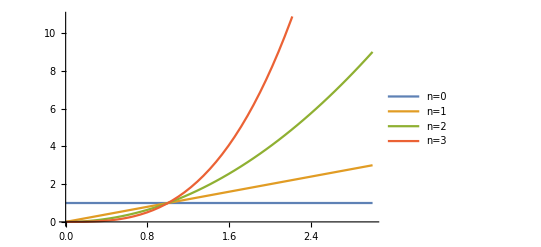

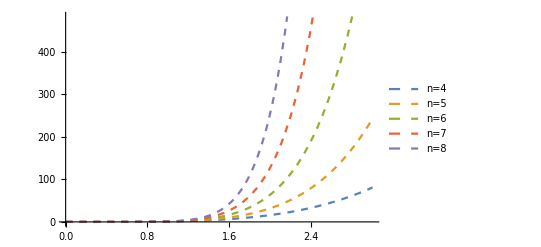

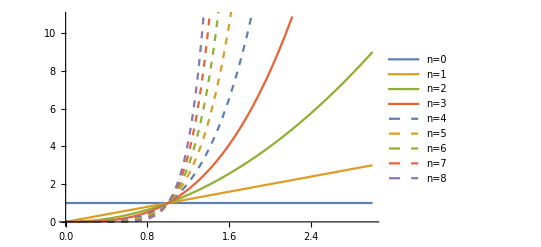

```mathematica
plot1=Plot[Evaluate[Table[x^n,{n,0,3}]],{x,0,3},LabelStyle->Small,PlotLegends->Table[StringForm["n=``",n],{n,0,3}]]
plot2=Plot[Evaluate[Table[x^n,{n,4,8}]],{x,0,3},PlotStyle->Dashed,LabelStyle->Small,PlotLegends->Table[StringForm["n=``",n],{n,4,8}]]
Show[plot1,plot2]
Clear[plot1,plot2]
```

## 1. q^2Mapping

### Compton Scattering

```mathematica
qsq[ω_,θ_]=ω^2(1-Cos[θ])
```

ω^2 (1-Cos[θ])

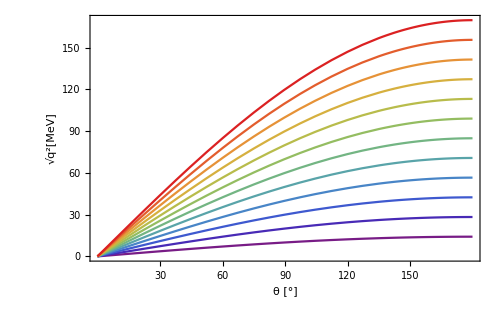

```mathematica
Plot[Evaluate[Table[Tooltip[√qsq[ω,θ Degree],StringForm["ω=``MeV",ω]],{ω,Table[10 i,{i,1,12}]}]],{θ,0,180 },ImageSize->500,Evaluate[plotoptions],FrameTicks->thetatables,FrameLabel->{"θ [°]","√(q^2)[MeV]"},PlotStyle->"Rainbow"]
```

#### Lines of constant qsquare in a θ-ω plot:

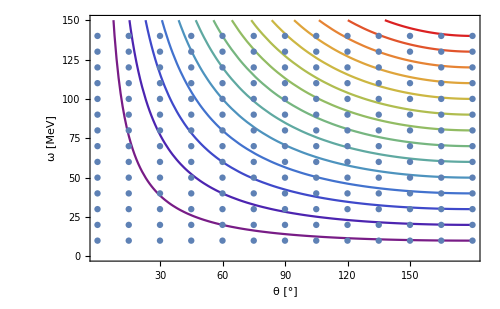
-Graphics- |

```mathematica
TableForm[{{Show[Plot[Evaluate[Table[Tooltip[(√qsquare)/(√(1-Cos[θ Degree])),StringForm["√(q^2)=``MeV",Round[1. √qsquare,0.01]]],{qsquare,Table[qsq[ω,180Degree],{ω,10,140,10}]}]],{θ,1,180},ImageSize->500,Evaluate[plotoptions],
PlotRange->{0,150},FrameTicks->thetatables,FrameLabel->{"θ [°]","ω [MeV]"},PlotStyle->"Rainbow"],
ListPlot[Flatten[Table[Tooltip[{θ,ω},StringForm["√(q^2)=``MeV",Round[√qsq[ω,θ Degree],10.^-4]]],{ω,10,140,10},{θ,0,180,15}],1]]],
LineLegend["Rainbow",Round[Table[√qsq[ω,180Degree],{ω,10,140,10}],10.^-4],LegendLabel->Style["lines of constant √(q^2) [MeV]",Larger],LegendLayout->{"Column",2},LabelStyle->Smaller]}}]
```